1266

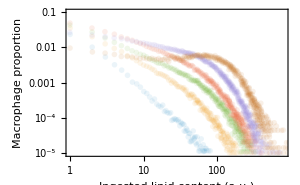

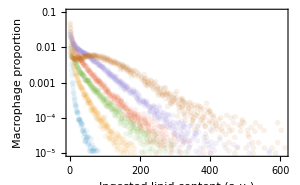

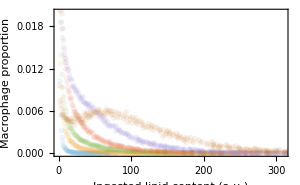

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,410},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[completeloglikelihood];

completeloglikelihood[{η_?NumericQ,e_?NumericQ,μ_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodM,loglikelihoodm,outcome,λ},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ,afun_?NumericQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
(*etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)*)
(*alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)>*)*)
conv=Prepend[Take[ListConvolve[fvec,v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
η/μ*afun *(conv-v)+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^2],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^(1/2)],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β1/(1+(β1-β0)/β0*Exp[-idx/q]));*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^q);*)

(*ηvec=A[t]*Developer`ToPackedArray@N@(Table[ηval,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t]],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η*A[t]), A[0]==0};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M, A},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48,60}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,6}];

loglikelihoodm=Sum[1/Length[resamples[[j]]]*Sum[-Log[resamples[[j]][[i]][[2]]*(1-resamples[[j]][[i]][[2]])*(σm*Sqrt[12*(j-1)])*Sqrt[2 Pi]]-1/(2*(σm*Sqrt[12*(j-1)])^2)*(Log[resamples[[j]][[i]][[2]]/(1-resamples[[j]][[i]][[2]])]-Log[moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]]/(1-moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]])])^2,{i,1,Length[resamples[[j]]]}],{j,2,6}];


If[outcome==0&&Element[loglikelihoodM+loglikelihoodm,Reals],loglikelihoodM+loglikelihoodm,-10^(6)]
]

(* Plot function *)

completeplots[{η_?NumericQ,e_?NumericQ,μ_?NumericQ, cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog,modelAplot},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ,afun_?NumericQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
(*etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)*)
(*alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)>*)*)
conv=Prepend[Take[ListConvolve[fvec,v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
η/μ*afun *(conv-v)+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^2],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^(1/2)],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β1/(1+(β1-β0)/β0*Exp[-idx/q]));*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^q);*)

(*ηvec=A[t]*Developer`ToPackedArray@N@(Table[ηval,{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t]],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η*A[t]), A[0]==0};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M, A},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];

modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,101}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean lipid content (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelAplot=Plot[{(A[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]]),(e+idx.(u[t]/. sol[[1]]))*(M[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]])},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.1}},PlotStyle->Automatic,ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Lipid content L (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];

Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot],modelAplot},{Show[distributionlinearplot,modeldistributionplot],Show[distributionloglinearplot,modeldistributionplotloglinear],Show[distributionloglogplot,modeldistributionplotloglog]}}]

]
```

```mathematica
(* β = β0 *)
nstep=1;
{ηval,eval,μval,cvval,β0val,σMval,σmval}={0.01,3,0.02423759173434658,1.1645730416201407,0.10277765163405865,2.999725307308357,0.010767833819977701,1.217742438624723,0.11774080416142488};
NMaximize[{completeloglikelihood[{η,100*e,100*μ,cv,β0,0,1,σM,σm}],0.01<η<30,0.01<e<3,0.01<μ<1, 0.5<cv<5,0.001<β0<1,0.01<σM<3,0.01<σm<1},{η,e,μ, cv,β0,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,μval,cvval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,μ,cv,β0,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

```mathematica
nstep=1;
{ηval,eval,μval,cvval,β0val,σMval,σmval}={0.01,3,0.10277765163405865,2.999725307308357,0.010767833819977701,1.217742438624723,0.11774080416142488};
FindMaximum[{completeloglikelihood[{0.01,100*3,100*μ,cv,β0,0,1,σM,σm}],0.001<μ<1, 0.5<cv<5,0.001<β0<1,0.01<σM<3,0.01<σm<1},{{μ,μval}, {cv,cvval},{β0,β0val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{ηval,eval,μ,cv,β0,σM,σm},completeloglikelihood[{0.01,100*3,100*μ,cv,β0,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.01,3,0.102778,2.99973,0.01099,1.21774,0.117741},38.5461}

Current x: {{0.01,3,0.107192,2.94829,0.0107859,1.22086,0.118851},38.548}

Current x: {{0.01,3,0.104697,2.97367,0.0107628,1.21855,0.117958},38.5493}

Current x: {{0.01,3,0.104416,2.97838,0.0107661,1.21853,0.117973},38.5494}

Current x: {{0.01,3,0.0989955,3.05444,0.010797,1.21775,0.117724},38.5499}

Current x: {{0.01,3,0.0988076,3.06012,0.0108007,1.21776,0.117735},38.5499}

Current x: {{0.01,3,0.0987859,3.06046,0.0108009,1.21776,0.117735},38.5499}

Current x: {{0.01,3,0.0987421,3.06113,0.0108012,1.21775,0.117733},38.5499}

Current x: {{0.01,3,0.0987422,3.06113,0.0108012,1.21775,0.117733},38.5499}

{38.5499,{μ→0.0987421664157426`11269033281263`,β0→0.01083.06113012,σM→1.21775,σm→0.117733}}

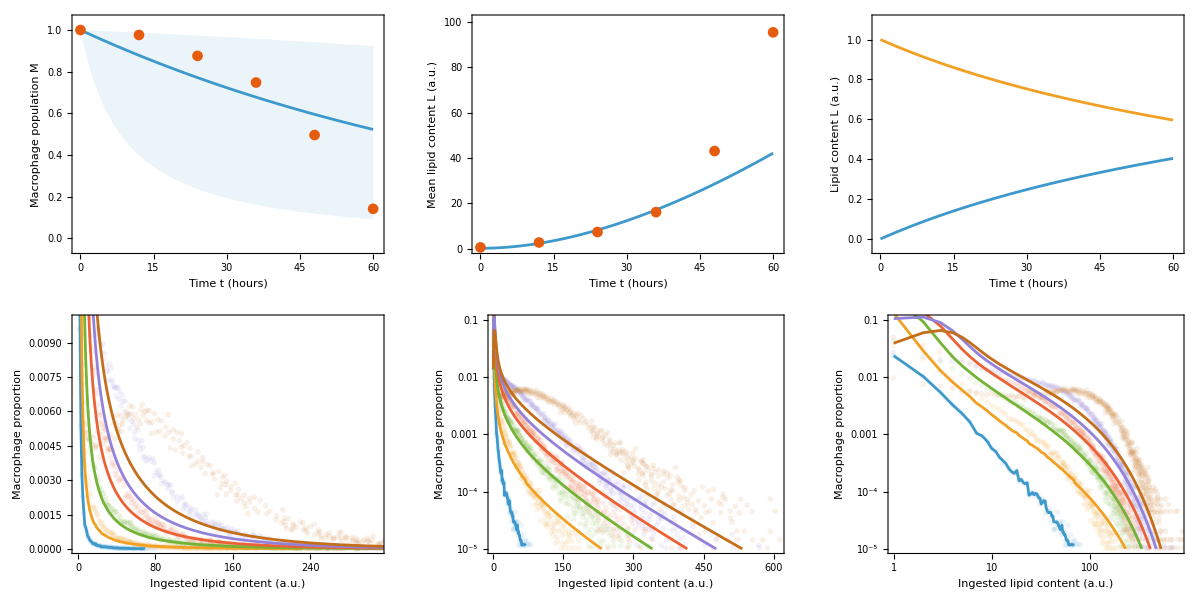

```mathematica
{ηval,eval,μval,cvval,β0val,σMval,σmval}={0.01,3,0.0987421664157426,3.0611269033281263,0.010801221202124595,1.217751164700878,0.11773333363869833};
completeplots[{ηval,100*eval,100*μval,cvval,β0val,0,1,σMval,σmval}]
```

```mathematica
(* β = β0*Exp [β1*t] *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}={3.0829850056779504,0.4097422269827945,0.2423677419132009,1.582880147630352,0.1533807223449481,0.07582162546755479,0.15988766860790493,0.12065804335391338};
NMaximize[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}],0.1<η<5,0.01<e<2,0.01<μ<1, 0.5<cv<3,0.01<β0<1,0.01<β1<0.3,0.01<σM<1,0.01<σm<1},{η,e,μ, cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

$Aborted

```mathematica
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}={0.26,1,0.24545910788346564,1.5757979903031405,0.15351295819953054,0.068,0.5,0.5};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}],0.1<η<100,0.01<e<2,0.01<μ<1, 0.5<cv<5,0.01<β0<1,0.01<β1<0.2,0.01<σM<1,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{ cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.178909,0.863526,0.176148,1.84914,0.150786,0.0764369,0.157908,0.0975042},49.7064}

Current x: {{0.178482,0.864622,0.176102,1.84935,0.150783,0.0764374,0.157906,0.0975044},49.7064}

Current x: {{0.178479,0.864631,0.176102,1.84935,0.150783,0.0764374,0.157906,0.0975045},49.7064}

{49.7064,{η→0.178479,e→0.864631,μ→0.176102,cv→1.84935}{η→0.178479,e→0.864631,μ→0.176102,cv→1.84935,β0→0.150783,β1→0.0764374,σM→0.157906,σm→0.0975045}}

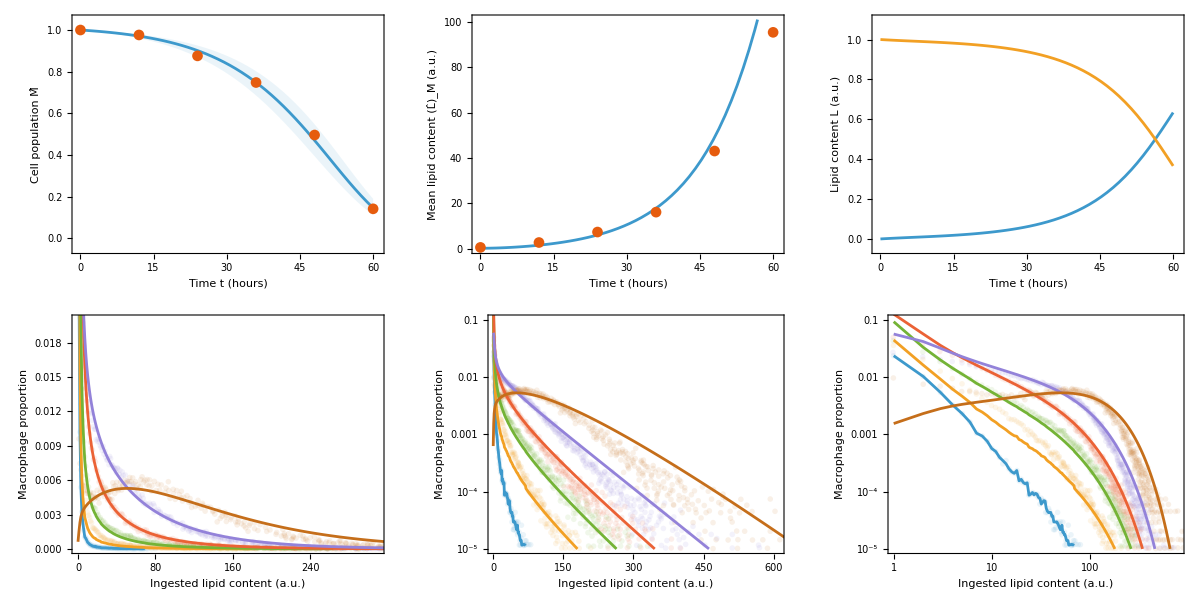

```mathematica
completeplots[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}/.{η->0.1784788636484224,e->0.8646311092862502,μ->0.17610220719546457,cv->1.849353933121796,β0->0.15078316467185318,β1->0.07643743377585485,σM->0.1579061199991276,σm->0.09750448015441675}]
```

```mathematica
(* β = β0 + β1*idx *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}={0.2615539812753046,1.0014409186580746,0.2543817668238998,1.8962397540039047,0.1511897291073227,0.12519608583946226,0.16585737490624927,0.08955628116339767};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}],0.01<η<5,0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.01<β1<1,0.01<σM<0.5,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

```mathematica
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}={0.2615539812753046,1.0014409186580746,0.2543817668238998,1.8962397540039047,0.1511897291073227,0.12519608583946226,0.16585737490624927,0.08955628116339767};
NMaximize[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}],0.01<η<5,0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.01<β1<1,0.01<σM<0.5,0.01<σm<1},{η,e,μ, cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,μval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.261554,1.00144,0.254382,1.89624,0.15119,0.125196,0.165857,0.0895563},49.8859}

{49.8859,{η→0.261554,e→1.00144,μ→0.254382,cv→1.89624,β0→0.15119,β1→0.125196,σM→0.165857,σm→0.0895563}}

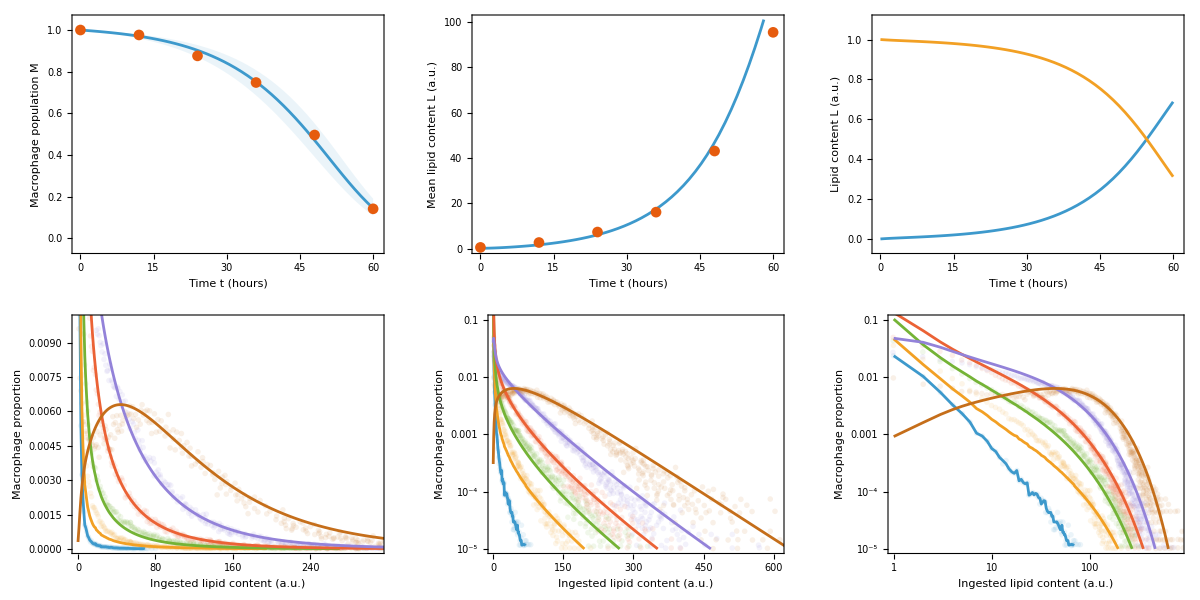

```mathematica
completeplots[{η,100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}/.{η->0.2615539812753046,e->1.0014409186580746,μ->0.2543817668238998,cv->1.8962397540039047,β0->0.1511897291073227,β1->0.12519608583946226,σM->0.16585737490624927,σm->0.08955628116339767}]
```

```mathematica
(* β =β1/(1+(β1-β0)/β0*Exp[-t/q]) -> tends to β1->infinity with LL < exponential case! *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.17873554891265667,0.8639648201394144,0.17637412394656274,1.847438613283898,0.15037281052089418,9.773103733126357,13.048363058378696,0.15789167247066732,0.09762914372398096};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}],0.01<η<5,0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.1<β1<100,0.01<σM<2,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,q,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.178736,0.863965,0.176374,1.84744,0.150373,9.7731,13.0484,0.157892,0.0976291},49.7006}

Current x: {{0.194796,0.824837,0.181322,1.81921,0.150989,9.85952,13.0667,0.159633,0.0984609},49.6972}

Current x: {{0.1879,0.841192,0.179195,1.83123,0.1506,11.7593,13.0595,0.158234,0.097768},49.7008}

Current x: {{0.182809,0.853259,0.178354,1.83621,0.151167,32.4979,13.1078,0.158264,0.097598},49.6993}

Current x: {{0.185625,0.847023,0.178679,1.83427,0.150796,38.5606,13.0772,0.158095,0.0977124},49.7044}

Current x: {{0.179427,0.861703,0.176542,1.84659,0.150709,42.674,13.0754,0.157951,0.0975492},49.7051}

Current x: {{0.179555,0.861897,0.176504,1.84695,0.150738,55.968,13.0778,0.157954,0.0975472},49.7054}

Current x: {{0.179552,0.861887,0.176502,1.84696,0.150749,55.968,13.0778,0.157959,0.0975453},49.7054}

$Aborted

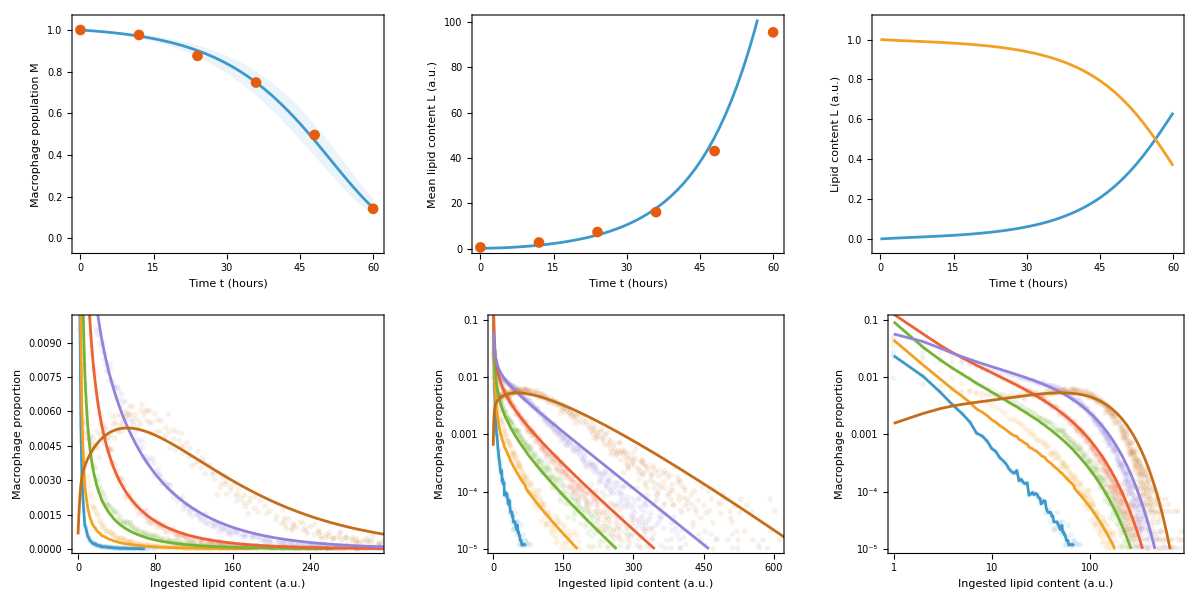

```mathematica
completeplots[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}/.{η->0.1795515476158156,e->0.8618869778378021,μ->0.17650175768531762,cv->1.846955279327083,β0->0.15074858148555897,β1->55.968007354743484,q->13.077757313942161,σM->0.15795884846127636,σm->0.09754529806189761}]
```

```mathematica
(* β=β1/(1+(β1-β0)/β0*Exp[-idx/q]: Saturating lipid-dependent death rate *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.12033604111040164,2.0388579800574957,0.390928863055435,1.7120935680928646,0.18597227204958983,0.5654252963341726,20.365589447000364,0.17773689194048012,0.07691780743229697};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}],0.01<η<5,0.01<e<3,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.1<β1<100,0.01<σM<2,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,q,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->3]
```

Current x: {{0.0972358,2.37339,0.370687,1.73195,0.186101,0.536293,20.0676,0.1774,0.0766324},50.3292}

Current x: {{0.0952213,2.41403,0.369703,1.73384,0.186083,0.535859,20.0717,0.177377,0.0766278},50.3312}

Current x: {{0.0952091,2.41429,0.369572,1.73387,0.186164,0.535876,20.0717,0.177413,0.0766222},50.3314}

Current x: {{0.0951681,2.41496,0.369522,1.7338,0.186172,0.535856,20.0717,0.177434,0.0766195},50.3314}

Current x: {{0.0950495,2.41736,0.369542,1.73367,0.186153,0.535915,20.0717,0.17743,0.076621},50.3315}

Current x: {{0.0950045,2.4181,0.369467,1.73354,0.186172,0.535721,20.0716,0.177438,0.0766168},50.3315}

Current x: {{0.0948772,2.42029,0.369218,1.73355,0.186219,0.535228,20.0714,0.177414,0.076585},50.3316}

Current x: {{0.0948257,2.42129,0.369394,1.7332,0.18618,0.535752,20.0713,0.177401,0.0765905},50.3316}

Current x: {{0.0948164,2.42173,0.369487,1.73316,0.186168,0.535641,20.0713,0.177392,0.0765943},50.3316}

Current x: {{0.0948105,2.42186,0.369493,1.73314,0.186167,0.535638,20.0713,0.17739,0.0765947},50.3316}

Current x: {{0.0947877,2.4224,0.369517,1.73316,0.186164,0.535587,20.0713,0.177386,0.0765961},50.3317}

Current x: {{0.094778,2.42256,0.369484,1.73316,0.186166,0.535564,20.0713,0.177387,0.0765951},50.3317}

Current x: {{0.0947535,2.42296,0.369448,1.73309,0.186176,0.535449,20.0713,0.177391,0.0765929},50.3317}

Current x: {{0.0946872,2.42437,0.369381,1.73327,0.186173,0.535379,20.0712,0.177391,0.0765926},50.3317}

Current x: {{0.094657,2.4249,0.369345,1.73333,0.186178,0.535398,20.0711,0.177392,0.0765918},50.3317}

Current x: {{0.0946457,2.4251,0.369323,1.73333,0.18618,0.535375,20.0711,0.177393,0.0765911},50.3317}

Current x: {{0.09461,2.42544,0.36897,1.73337,0.186243,0.53466,20.0711,0.177423,0.0765761},50.3318}

$Aborted

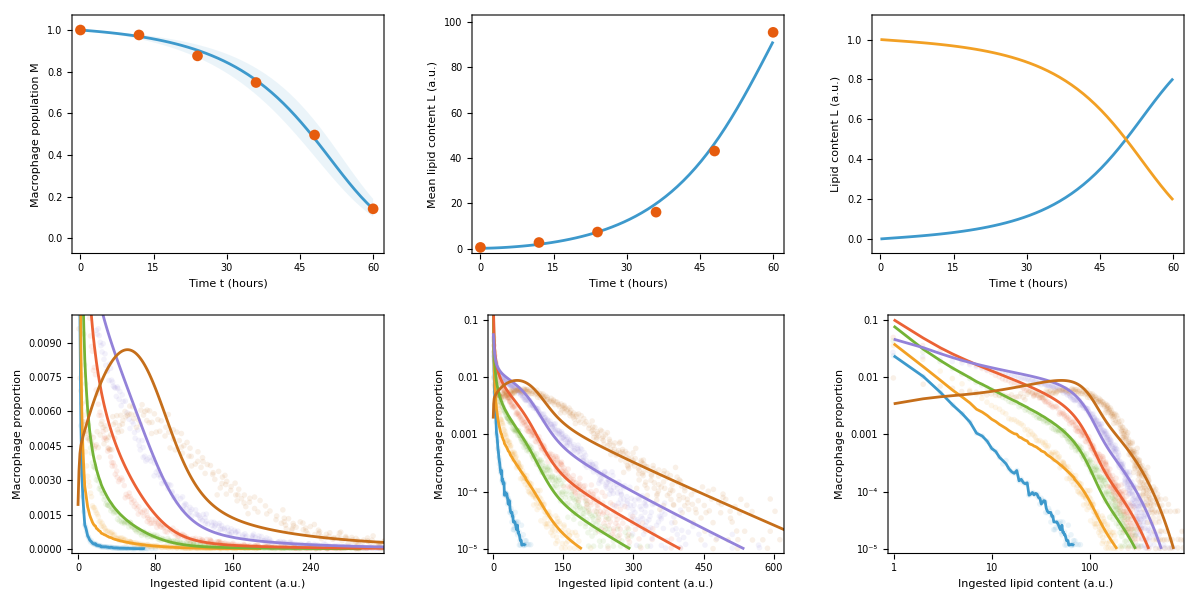

```mathematica
completeplots[{η,100*e,100*μ,cv,β0/100,β1,q,σM,σm}/.{η->0.09460996010371917,e->2.42543681321573,μ->0.36897013580798965,cv->1.7333747134323303,β0->0.18624323118966882,β1->0.5346595024575225,q->20.07105616968132,σM->0.17742304955828092,σm->0.07657606752144236}]
```

```mathematica
(* β = β0+(β1-β0)*(1-Exp[-idx/q]: Saturating lipid-dependent death rate *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.09460996010371917,0.9,0.36897013580798965,1.7333747134323303,0.12,15,5,1,0.1};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}],0.01<η<5,0.01<e<3,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.1<β1<100,0.01<σM<2,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,q,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->3]
```

Current x: {{0.257524,0.984378,0.254211,1.81062,0.148117,90.1778,661.131,0.165779,0.0889789},49.9207}

Current x: {{0.257524,0.984378,0.254211,1.81062,0.148117,90.1778,661.131,0.165779,0.0889789},49.9207}

Current x: {{0.257524,0.984378,0.254211,1.81062,0.148117,90.1778,661.131,0.165779,0.0889789},49.9207}

«5 more identical outputs»

Current x: {{0.257239,0.984034,0.253773,1.81063,0.14831,90.1789,661.131,0.165836,0.0889471},49.9207}

Current x: {{0.257774,0.983875,0.254279,1.8103,0.148118,90.1979,661.276,0.165775,0.0889795},49.9207}

Current x: {{0.257574,0.9843,0.254185,1.8107,0.14812,90.1758,661.148,0.165778,0.088979},49.9207}

Current x: {{0.257573,0.984303,0.254183,1.8107,0.148119,90.1758,661.148,0.165776,0.088978},49.9207}

{49.9207,{η→0.257573,e→0.984303,μ→0.254183,cv→1.8107,β0→0.148119,β1→90.1758,q→661.148,σM→0.165776,σm→0.088978}}

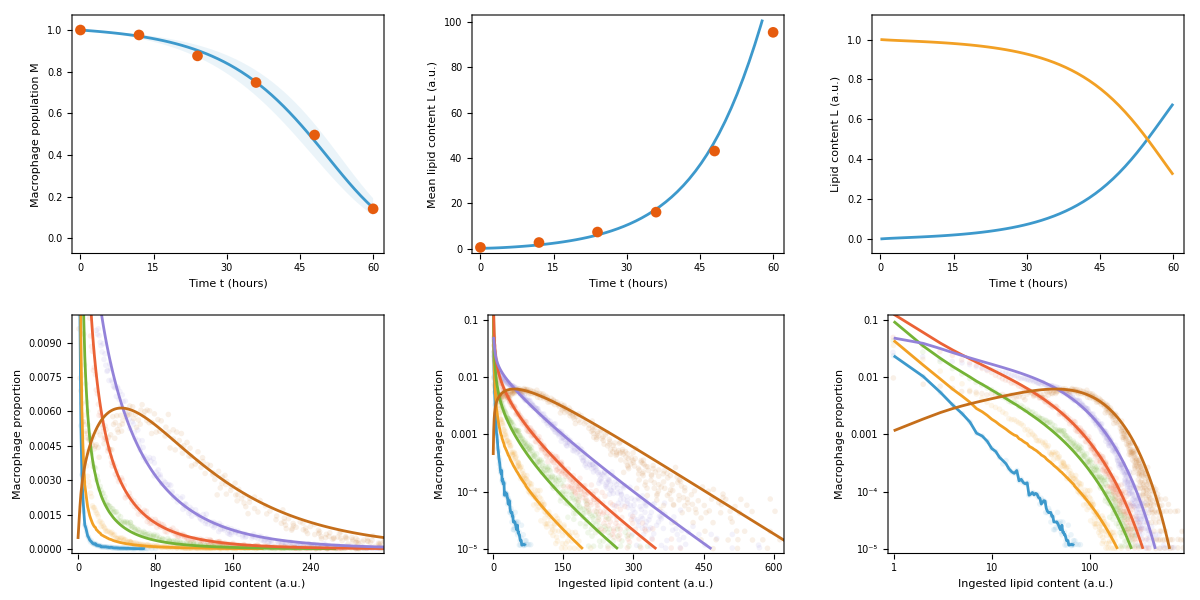

```mathematica
completeplots[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}/.{η->0.257573339901462,e->0.9843025325106832,μ->0.25418337771057736,cv->1.810701405582803,β0->0.14811930948434696,β1->90.17576276211271,q->661.1484787720814,σM->0.16577642876597862,σm->0.08897795307741835}]
```

```mathematica
(* β = β0 + β1*idx^q *)
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.2615539812753046,1.0014409186580746,0.2543817668238998,1.8962397540039047,0.1511897291073227,0.12519608583946226,1,0.16585737490624927,0.08955628116339767};
NMaximize[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}],0.01<η<5,0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.01<β1<1,0.1<q<3,0.01<σM<0.5,0.01<σm<1},{η,e,μ, cv,β0,β1,q,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,q,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

$Aborted

```mathematica
nstep=1;
{ηval,eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.2615539812753046,1.0014409186580746,0.2543817668238998,1.8962397540039047,0.1511897291073227,0.12519608583946226,1,0.16585737490624927,0.08955628116339767};
FindMaximum[{completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}],0.01<η<5,0.01<e<2,0.01<μ<1,0.5<cv<3,0.1<β0<1,0.01<β1<1,0.1<q<3,0.01<σM<0.5,0.01<σm<1},{{η,ηval},{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,μ,cv,β0,β1,q,σM,σm},completeloglikelihood[{η,100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.264882,1.00918,0.262944,1.90767,0.155806,0.0986413,1.05563,0.166867,0.0887599},49.9063}

Current x: {{0.264882,1.00918,0.262944,1.90767,0.155806,0.0986413,1.05563,0.166867,0.0887599},49.9063}

Current x: {{0.264882,1.00918,0.262944,1.90767,0.155806,0.0986413,1.05563,0.166867,0.0887599},49.9063}

$Aborted

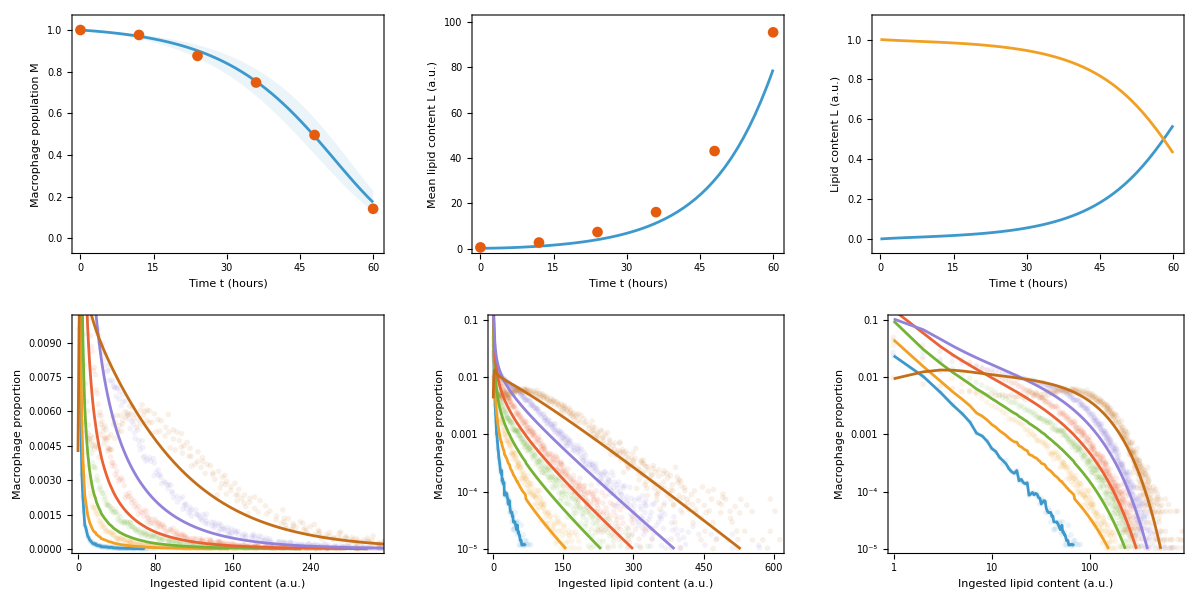
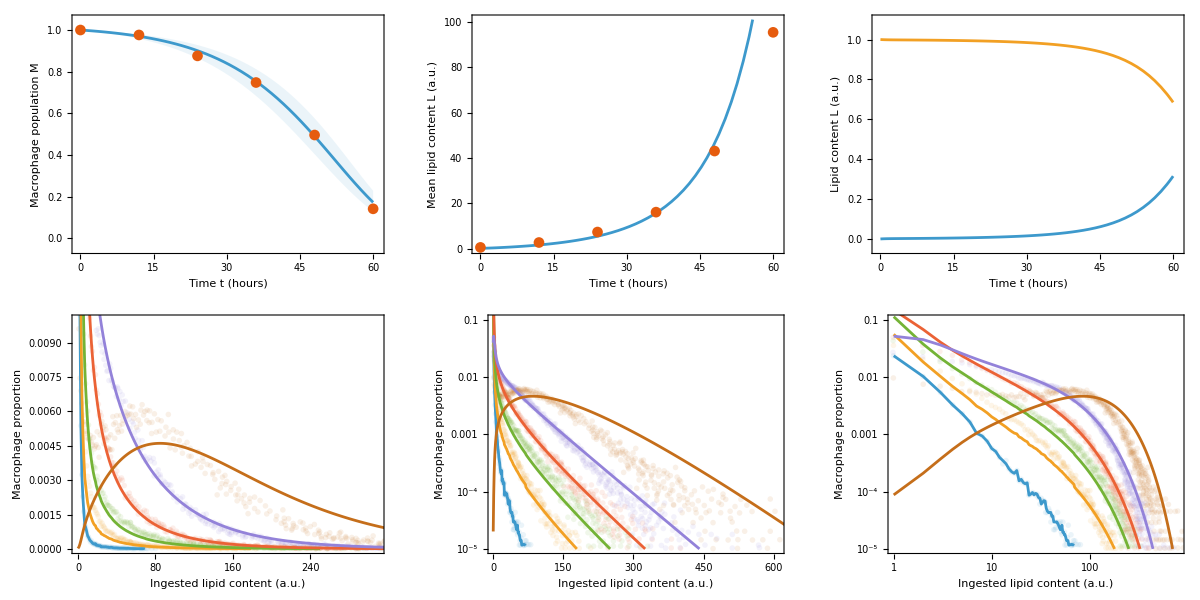
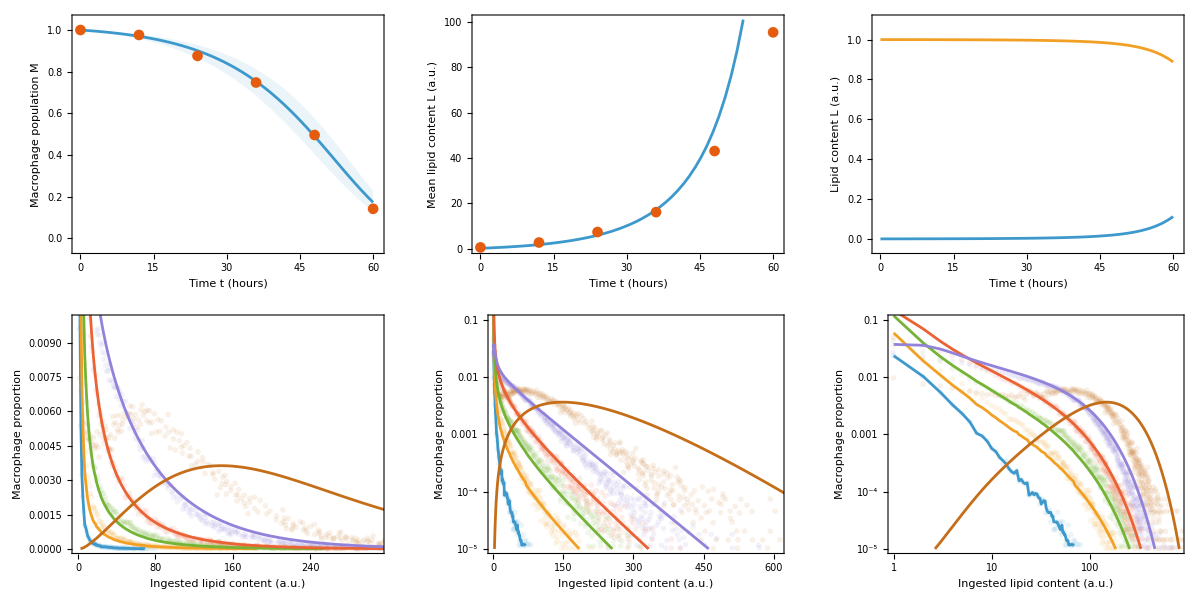

```mathematica
Table[completeplots[{η,100*e,100*μ,cv,β0/100,β1,1,σM,σm}/.{η->val,e->0.5286062183817707,μ->0.1455088428748961,cv->1.9993747328174223,β0->0.15872415807247975,β1->0.07345566803880664,σM->0.17706496337029562,σm->0.08619177018275748}],{val,{0.2,1,5}}]
```

```mathematica
(* Extending the quasi-steady selected model to t=60 *)

(* Plot function *)

QSSAextension[{{η1_?NumericQ,η2_?NumericQ,η3_?NumericQ},e_?NumericQ,μ_?NumericQ, cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog,modelAplot,consplot,eqs1,eqs2,eqs3,sol1,sol2,sol3,moutput1,moutput2,moutput3,modeldistributionplotloglinear1,modeldistributionplotloglinear2,modeldistributionplotloglinear3},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ,afun_?NumericQ,etaval_?NumericQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
(*etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)*)
(*alpha=Dot[βvec*(ee+idx),v];(* <beta_i (e+i)>*)*)
conv=Prepend[Take[ListConvolve[fvec,v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
etaval/μ*afun *(conv-v)+(betaBar-βvec)*v
];

imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^2],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^(1/2)],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);
(*βvec=Developer`ToPackedArray@N@(β1/(1+(β1-β0)/β0*Exp[-idx/q]));*)
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^q);*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];

eqs1={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t],η1],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η1*A[t]), A[0]==0};
eqs2={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t],η2],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η2*A[t]), A[0]==0};
eqs3={u'[t]==rhsVecfunction[u[t],βvec,fvec,e,μ,idx,n,A[t],η3],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1,A'[t]==M[t]*(Dot[βvec*(e+idx),u[t]]-η3*A[t]), A[0]==0};

sol1=NDSolve[{eqs1(*,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]*)},{u,M, A},{t,0,tmax}];
sol2=NDSolve[{eqs2(*,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]*)},{u,M, A},{t,0,tmax}];
sol3=NDSolve[{eqs3(*,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]*)},{u,M, A},{t,0,tmax}];

moutput1=Table[u[t]/. sol1[[1]],{t,{0,12,24,36,48,60}}];
moutput1=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput1}];

moutput2=Table[u[t]/. sol2[[1]],{t,{0,12,24,36,48,60}}];
moutput2=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput2}];

moutput3=Table[u[t]/. sol3[[1]],{t,{0,12,24,36,48,60}}];
moutput3=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput3}];

(*modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];*)
modeldistributionplotloglinear1=ListPlot[moutput1,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglinear2=ListPlot[moutput2,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglinear3=ListPlot[moutput3,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
(*modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];*)


consplot=Show[ListPlot[Table[{12*(i-1),Mdata[[i]][[2]]*(1+lipiddata[[i]][[2]]/e)/(1+lipiddata[[1]][[2]]/e)}/.{e->100*0.5474411415249859},{i,1,6}],PlotRange->{{0,60.5},{0.0,1.05}},Frame->True,PlotMarkers->Automatic,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Total cell lipid L_M(t)/L_M(0)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},(*PlotLegends->{"μ_e = 55 a.u."},*)ImageSize->300,PlotTheme->"Scientific"],Plot[Evaluate@Table[M[t]*(1+1/e*(idx.u[t]))/(1+1/e*(idx.u[0]))/.{s[[1]]},{s,{sol1,sol2,sol3}}],{t,50,65},PlotStyle->{{Automatic},{Automatic,Dashed},{Automatic,DotDashed}},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},BaseStyle->{FontFamily->"Cambria Math"},PlotLegends->{"η = 1","η = 0.1","η = 0.01"}],Plot[Evaluate@Table[M[t]*(1+1/e*(idx.u[t]))/(1+1/e*(idx.u[0]))/.{s[[1]]},{s,{sol1,sol2,sol3}}],{t,0,50},PlotStyle->{{Automatic},{Automatic,Dashed},{Automatic,DotDashed}}],ListPlot[Table[{12*(i-1),Mdata[[i]][[2]]*(1+lipiddata[[i]][[2]]/e)/(1+lipiddata[[1]][[2]]/e)}/.{e->100*0.5474411415249859},{i,1,6}],PlotRange->{{-0.5,65},{0.0,1.25}},Frame->True,PlotMarkers->Automatic,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Total macrophage lipid content"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},(*PlotLegends->{"μ_e = 55 a.u."},*)ImageSize->300,PlotTheme->"Scientific"]];

modelMplot=Show[Plot[Evaluate@Table[M[t]/.s[[1]],{s,{sol1,sol2,sol3}}],{t,0,60.5},PlotRange->{{-0.5,60.5},{-0.05,1.05}},PlotStyle->{{Automatic},{Automatic,Dashed},{Automatic,DotDashed}},ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True],Mplot];

modelLplot=Show[Plot[Evaluate@Table[idx.(u[t]/. s[[1]]),{s,{sol1,sol2,sol3}}],{t,0,60.5},PlotRange->{{-0.5,60.5},{-0.05,101}},PlotStyle->{{Automatic},{Automatic,Dashed},{Automatic,DotDashed}},ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean ingested lipid (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True],Lplot];

Grid[{{consplot,modelMplot},{modelLplot,Show[distributionloglinearplot,modeldistributionplotloglinear1]}}]

]
```

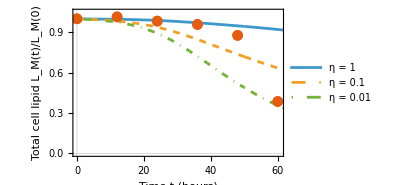
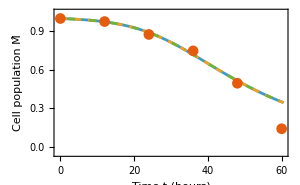
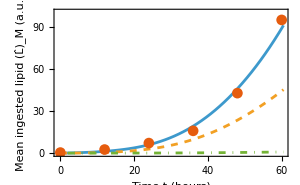
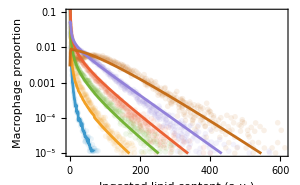
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* version with time-dependent death *)
QSSAextension[{{η1,η2,η3},100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}/.{η1->1,η2->0.1,η3->0.001,e->0.5474411415249859,μ->0.1540017845063153,cv->1.901727155522228,β0->0.10151531079350407,β1->3.37316547096781,q->8.331547512030825,σM->0.11975004073712367,σm->0.08933492225016373}]
```

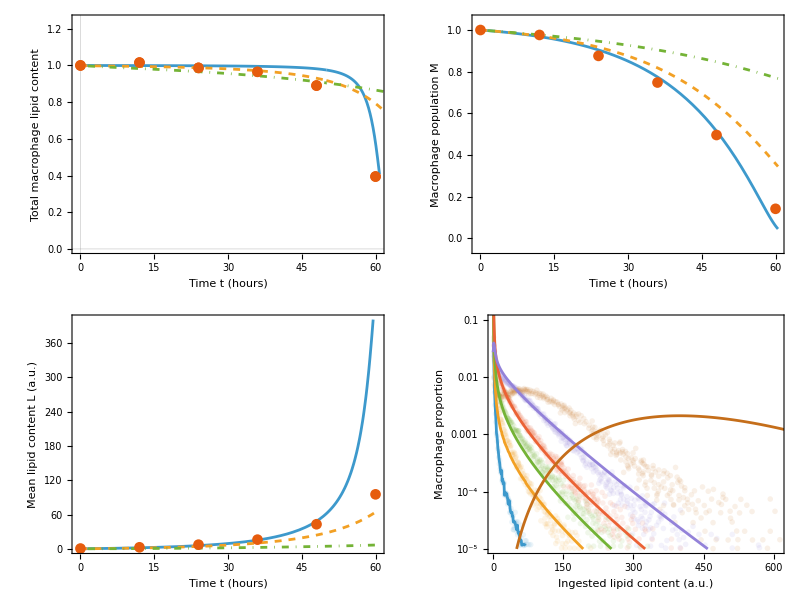

```mathematica
(* version with lipid-dependent death *)
QSSAextension[{{η1,η2,η3},100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}/.{η1->10,η2->1,η3->0.1,e->0.5287129603284024,μ->0.2160087910332719,cv->1.9686094388949378,β0->0.15471757762320495,β1->0.11625650359165779,σM->0.21134634888711168,σm->0.08604293379046177}]
```